## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0025;horizSize=0.01;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/22/tables/data.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data//TableForm
```

n | lam | al | 
1. | 7032. | 2601. | 5.
2. | 6929. | 2577. | 5.
3. | 6717. | 2509. | 5.
4. | 6678. | 2498. | 5.
5. | 6599. | 2470. | 5.
6. | 6533. | 2447. | 5.
7. | 6507. | 2442. | 5.
8. | 6402. | 2400. | 5.
9. | 6383. | 2395. | 5.
10. | 6334. | 2395. | 5.
11. | 6305. | 2360. | 5.
12. | 6267. | 2349. | 5.
13. | 6217. | 2328. | 5.
14. | 6164. | 2306. | 5.
15. | 6143. | 2297. | 5.
16. | 6096. | 2277. | 5.
17. | 6074. | 2266. | 5.
18. | 6030. | 2248. | 5.
19. | 5976. | 2219. | 5.
20. | 5945. | 2207. | 5.
21. | 5882. | 2177. | 5.
22. | 5852. | 2160. | 5.
23. | 5401. | 1898. | 5.
24. | 5341. | 1862. | 5.
25. | 5331. | 1852. | 5.
K1 | 6907. | 2564. | 5.
K2 | 6234. | 2330. | 5.
1. | 5791. | 2125. | 5.
2. | 5770. | 2115. | 5.
3. | 5460. | 1934. | 5.
4. | 4916. | 1516. | 5.
5. | 4358. | 856. | 5.
6. | 4047. | 306. | 5.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitG=data⟦2;;,{3,2}⟧;
fitG=LinearModelFit[forFitG,{1,x,x^2},x]
fitG@"ParameterTable"
Plot[fitG["Function"]@x, {x, 0, 3000}]
```

```mathematica
model =c/(x-X)+λ
```

c/(x-X)+λ

```mathematica
fit=NonlinearModelFit[forFitG,model,{c,X,λ},x]
fit@"ParameterTable"
```

FittedModel[2341.22-(6.19529×10^6)/(-3925.84+x)]

| Estimate | Standard Error | t-Statistic | P-Value
c | -6.19529×10^6 | 134283. | -46.1362 | 2.02771×10^-29
X | 3925.84 | 20.1002 | 195.313 | 3.88754×10^-48
λ | 2341.22 | 35.4814 | 65.9845 | 4.89771×10^-34

```mathematica
{{c, -6.195288446983178*^6, 134282.65062902204}, {X, 3925.8418988560584, 20.100244324378785}, {λ, 2341.219292898522, 35.481367782165094}}
```

{{c,-6.19529×10^6,134283.},{X,3925.84,20.1002},{λ,2341.22,35.4814}}

```mathematica
TeXForm[{{c,-6.195288446983178*^6,134282.65062902204},{X,3925.8418988560584,20.100244324378785},{λ,2341.219292898522,35.481367782165094}}]
```

\left(
\begin{array}{ccc}
 c & -6.19529\times 10^6 & 134283. \\
 X & 3925.84 & 20.1002 \\
 \lambda  & 2341.22 & 35.4814 \\
\end{array}
\right)

```mathematica
print@x_:=(Print@x;x);
```

```mathematica
forFitECr=datad⟦2;;,-1⟧
```

{10.26,11.07,12.42,5.13,9.18}

```mathematica
χ=Total[(print@fitE["FitResiduals"]/print@forFitECr)^2]/(Length[forFitE]-2)
χ^2
```

{20.008,20.6005,-18.3834,-38.3806,16.1555}

{10.26,11.07,12.42,5.13,9.18}

22.8427

521.79

```mathematica
FittedModel[2341.219292898522-(6.195288446983178*^6)/(-3925.8418988560584+x)]
```

FittedModel[2341.22-(6.19529×10^6)/(-3925.84+x)]

```mathematica
%51["Function"]
```

2341.22-(6.19529×10^6)/(-3925.84+#1)&

```mathematica
(2341.219292898522-(6.195288446983178*^6)/(-3925.8418988560584+#1)&)[1616]
```

5023.35

```mathematica
(2341.219292898522-(6.195288446983178*^6)/(-3925.8418988560584+#1)&)[2282]
```

6110.01

```mathematica
(2341.219292898522-(6.195288446983178*^6)/(-3925.8418988560584+#1)&)[2386]
```

6364.55

```mathematica
(2341.219292898522-(6.195288446983178*^6)/(-3925.8418988560584+#1)&)[415]
```

4105.84

```mathematica
(2341.219292898522-(6.195288446983178*^6)/(-3925.8418988560584+#1)&)[838]
```

4347.57

```mathematica
(2341.219292898522-(6.195288446983178*^6)/(-3925.8418988560584+#1)&)[1464]
```

4857.75

```mathematica
(2341.219292898522-(6.195288446983178*^6)/(-3925.8418988560584+#1)&)[2452]
```

6544.72

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,250}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,200}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

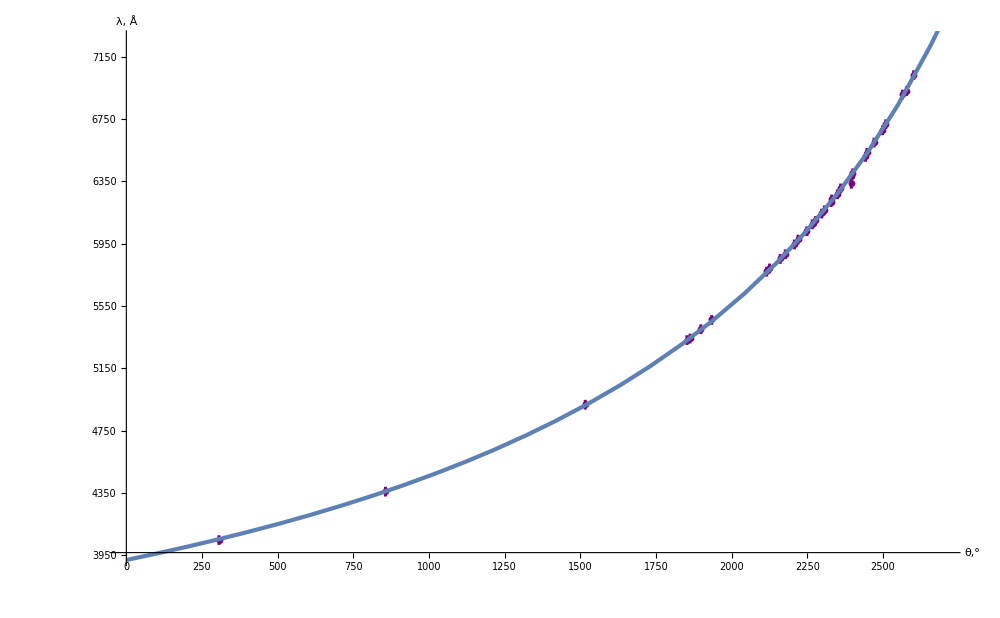

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{3,2,4,4}⟧,
GridLines->{grids@50,grids@100},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"θ,°","λ, Å"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.007,
(*vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),*)
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX,myTicY},
PlotRange->{{0,2700},{3950,7250}}], 
Plot[fit["Function"]@x,{x,0,5000}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXg=MapAt[dropLastDot@*ToString,data⟦2;;,{1,2,3}⟧];
forTeXg//TeXForm
```

\text{MapAt}\left[\text{dropLastDot}\text{@*}\text{ToString},\left(
\begin{array}{ccc}
 1. & 7032. & 2601. \\
 2. & 6929. & 2577. \\
 3. & 6717. & 2509. \\
 4. & 6678. & 2498. \\
 5. & 6599. & 2470. \\
 6. & 6533. & 2447. \\
 7. & 6507. & 2442. \\
 8. & 6402. & 2400. \\
 9. & 6383. & 2395. \\
 10. & 6334. & 2395. \\
 11. & 6305. & 2360. \\
 12. & 6267. & 2349. \\
 13. & 6217. & 2328. \\
 14. & 6164. & 2306. \\
 15. & 6143. & 2297. \\
 16. & 6096. & 2277. \\
 17. & 6074. & 2266. \\
 18. & 6030. & 2248. \\
 19. & 5976. & 2219. \\
 20. & 5945. & 2207. \\
 21. & 5882. & 2177. \\
 22. & 5852. & 2160. \\
 23. & 5401. & 1898. \\
 24. & 5341. & 1862. \\
 25. & 5331. & 1852. \\
 \text{K1} & 6907. & 2564. \\
 \text{K2} & 6234. & 2330. \\
 1. & 5791. & 2125. \\
 2. & 5770. & 2115. \\
 3. & 5460. & 1934. \\
 4. & 4916. & 1516. \\
 5. & 4358. & 856. \\
 6. & 4047. & 306. \\
\end{array}
\right)\right]

### Импорт табличных данных

```mathematica
dataR=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/22/tables/mn.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataR//TableForm
```

n | al | l |  |  |  | 
a | 2452. | 6544. | 3. | 0.139 | 1.528 | 0.046
b | 1464. | 4857. | 4. | 0.188 | 2.059 | 0.062
g | 838. | 4347. | 5. | 0.21 | 2.3 | 0.069
d | 415. | 4105. | 6. | 0.222 | 2.436 | 0.073

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.0170091+10.8823 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0170091 | 0.00531635 | 3.19939 | 0.0853692
x | 10.8823 | 0.027645 | 393.646 | 6.45334×10^-6

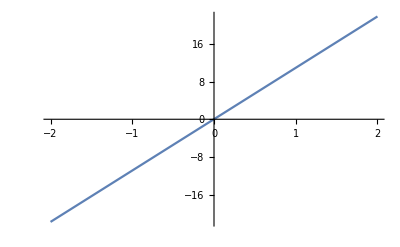

```mathematica
forFitR=dataR⟦2;;,{5,6}⟧;
fitR=LinearModelFit[forFitR,{1,x},x]
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, -2, 2}]
```

```mathematica
{{1, 0.017009083201946718, 0.0053163452090220255}, {x, 10.88232912323785, 0.027644986170554692}}
```

{{1,0.0170091,0.00531635},{x,10.8823,0.027645}}

```mathematica
TeXForm[{{1,0.017009083201946718,0.0053163452090220255},{x,10.88232912323785,0.027644986170554692}}]
```

\left(
\begin{array}{ccc}
 1 & 0.0170091 & 0.00531635 \\
 x & 10.8823 & 0.027645 \\
\end{array}
\right)

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX2235[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.25}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

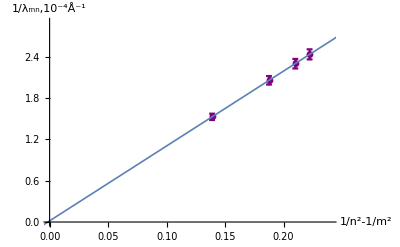

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{5,6,7,7}⟧,
GridLines->{grids@0.02,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"1/n^2-1/m^2","1/λ_mn,10^-4Å^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)(*,
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
(*Ticks->{myTicX2235,Automatic},*)
PlotRange->{{0,0.24},{0,2.9}}], 
Plot[fitR["Function"]@x,{x,-35,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXR=MapAt[dropLastDot@*ToString,dataR,{{2;;,All}}];
forTeXR//TeXForm
```

\left(
\begin{array}{ccccccc}
 \text{n} & \text{al} & \text{l} & \text{} & \text{} & \text{} & \text{} \\
 \text{a} & 2452 & 6544 & 3 & 0.139 & 1.528 & 0.046 \\
 \text{b} & 1464 & 4857 & 4 & 0.188 & 2.059 & 0.062 \\
 \text{g} & 838 & 4347 & 5 & 0.21 & 2.3 & 0.069 \\
 \text{d} & 415 & 4105 & 6 & 0.222 & 2.436 & 0.073 \\
\end{array}
\right)

```mathematica
0.523701941038647*10^-15*1.6021766208*10^-19
```

8.39063×10^-35

```mathematica
0.1754458528429999/0.523701941038647
```

0.335011

```mathematica
0.3350108890088164*8.390630061997003*^-35
```

2.81095×10^-35

```mathematica
0.9491845318387957/0.523701941038647
```

```mathematica
(2*Pi*3*10^8)/(1.812451811723856*10^15)
```

1.04×10^-6

```mathematica
Sqrt[0.3350108890088164^2+(0.5507171072421373/0.9491845318387957)^2]
```

```mathematica
0.6699736050362773
```

```mathematica
{{10.88232912323785, 0.027644986170554692}}
```

```mathematica
10.88232912323785*10^-4*10^8
```

108823.

```mathematica
0.027644986170554692*10^4
```

276.45